# NG_4 T_02. Наивный байесовский классификатор

КМ2021, курс 2, семестр 4
Шпак Андрей.
16-фев-2023

Гистограмма.

Сначала я разобрался, что же все таки представляет собой набор Train. Проанализировав пункты 1.2, 1.4 раздела “Советы и подсказки” а так же код функции LoadMNIST, я пришел к выводу, что это это выражение, которое содержит два вложенных списка в список. Первый из вложенных — это цифры, а второй - соответствующие цифре растровые объекты.

Поэтому, с помощью Position могу получить все позиции, на которых расположилось мое число — 2, при этом оперирую первым вложенным списком.

```mathematica
friendPos=Position[Train[[1]],2]
```

Теперь можно получить соответствующие значения пикселей у каждого Friend объекта на 9 строке и 10 столбце во втором вложенном списке Train. Но сначала я столкнулся с тем, что сами растровые объекты представлены в виде списка значений, а не матрицы значений. Поэтому преобразовал список в матрицу с помощью ArrayReshape. Растры представляют собой квадратные матрицы размерностью 28 на 28. Подходящие мне объекты получаю как раз благодаря уже известным позициям, посчитанным в выражении friendPos.

```mathematica
fixedPixelFriendValue=ArrayReshape[Train[[2,#]],{28,28}][[9,10]]&/@friendPos;
```

Теперь те же самые действия выполняю, но с Foe объектами.  Была проблема с описанием паттерна выбора не двоек. Решение нашел тут: https://mathematica.stackexchange.com/questions/180/how-to-find-the-position-of-elements-in-a-list-satisfying-criteria

```mathematica
foePos=Position[Train[[1]],_?(#!=2&)]
```

```mathematica
fixedPixelFoeValue=ArrayReshape[Train[[2,#]],{28,28}][[9,10]]&/@foePos;
```

И сама гистограмма данных. Возможно, я бы выдвинул предположение, что данные по Friend объектам и по Foe объектам различаются в какое-то k раз. Ну и, конечно, видно, что нулевых значений больше в обоих наборах данных.

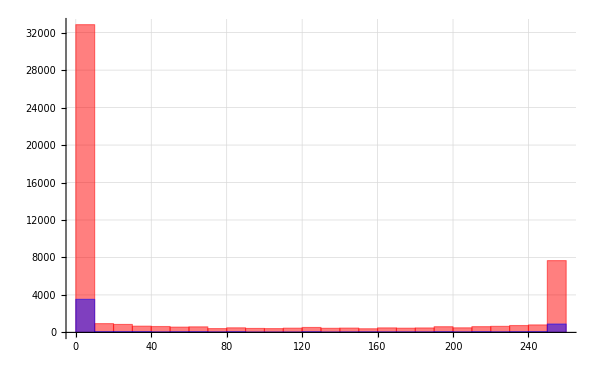

```mathematica
Histogram[{fixedPixelFoeValue,fixedPixelFriendValue},ChartStyle->{Red,Blue},GridLines->Automatic,ImageSize->600]
```

## Советы и подсказки

### Subsection. Загрузка базы растров MNIST

В каталоге  MNIST (см.[1]) приведены растры 28×28 рукописных цифр “0”–“9”.  База данных каталога находится в файлах: “train-images.idx3-ubyte”, “train-labels.idx1-ubyte” — 60 000 образцов тренировочного набора (Train) и “t10k-images.idx3-ubyte”, “t10k-labels.idx1-ubyte” — 10 000 образцов тестового набора (Test). Сами файлы и описание их структуры можно найти на сайте http://yann.lecun.com/exdb/mnist/index.html.

```mathematica
SetDirectory@NotebookDirectory[];
```

#### Subsection.Subsubsection. Загрузка набора растров ИмяНабора↦{Цифры,Растры}

```mathematica
ClearAll[LoadMNIST];
LoadMNIST[SetName_String]:=Module[{F,FDummy,Counter,Rows,Cols,Digits,Images},
F=OpenRead[ToLowerCase[SetName]<>"-images.idx3-ubyte",BinaryFormat->True];
{FDummy,Counter,Rows,Cols}=BinaryRead[F,Array["Integer32"&,4],ByteOrdering->+1];
Images=Partition[BinaryReadList[F,"Byte",ByteOrdering->+1],Rows Cols];
Close[F];
F=OpenRead[ToLowerCase[SetName]<>"-labels.idx1-ubyte",BinaryFormat->True];
{FDummy,Counter}=BinaryRead[F,Array["Integer32"&,2],ByteOrdering->+1];
Digits=BinaryReadList[F,"Byte",ByteOrdering->+1];
Close[F];
{Digits,Images}]
```

#### Subsection.Subsubsection. Загрузка тренировочных шаблонов TrainLabel→TrainImage

```mathematica
Map[Dimensions,Train=LoadMNIST["train"]]
```

{{60000},{60000,784}}

#### Subsection.Subsubsection. Загрузка проверочных шаблонов TestLabel→TestImage

```mathematica
Map[Dimensions,Test=LoadMNIST["t10k"]]
```

{{10000},{10000,784}}

#### Subsection.Subsubsection. Загруженные наборы шаблонов

```mathematica
DynamicModule[{m=4},Grid[{
{Row@{"Magnification: ",SetterBar[Dynamic@m,Range[10]]},SpanFromLeft},{
Manipulate[Style[Train⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Train⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,6,"Train"},1,Length@Train⟦1⟧,1,Appearance->"Labeled"},Paneled->False],
Manipulate[Style[Test⟦1,n⟧,Bold,24+2m]->Image[Partition[256-Test⟦2,n⟧,28],"Byte",ColorSpace->"GrayScale",Magnification->m],{{n,4655,"Test"},1,Length@Test⟦1⟧,1,Appearance->"Labeled"},Paneled->False]}},Frame->All,FrameStyle->Gray]]
```